## Gauss-Seidel

```mathematica
gs[mat_,b_,xi_,n_,pre_]:=Module[{lb=Length[b]},{x[1],x[2],x[3]}=SetPrecision[{xi[[1]],xi[[2]],xi[[3]]},pre];
																				               (*## &[]] quita todo los nulls que se generan en el programa*)
Table[x[i]=1/mat[[i,i]](b[[i]]-∑_(j=1)^lb If[i≠j,mat[[i,j]]x[i],##&[]]),{n},{i,lb}];Table[x[k],{k,lb}]
]
```

```mathematica
gs[mat=({{3, 1, -1}, {2, 5, -3}, {1, 8, -12}}),b=(-{{1}, {9}, {8}}),{1,2,3},30,20]
```

(-0.333333333333333333333333
-2.25
2.6667261940300566715768)

#### Newton Raphson

```mathematica
$PrePrint=TraditionalForm
```

TraditionalForm

```mathematica
Clear[x];
```

#### ejercicio 15 (a)

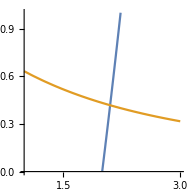

```mathematica
(*graficar para poder encontrar puntos iniciales*)
ContourPlot[{x^2-y ==4, ⅇ^-x+x y==1},{x,1,3},{y,0,1},Frame->False,Axes->True]
```

```mathematica
(*definimos las funciones*)
f=({{x^2-y^2-4}, {ⅇ^-x+x y-1}});x0=({{2.0}, {0.4}});
Table[feva= f/.{x->x0[[1,1]],y->x0[[2,1]]};
jac=({{D[f[[1,1]], x], D[f[[1,1]], y]}, {D[f[[2,1]], x], D[f[[2,1]], y]}});
jaceva=jac/.{x->x0[[1,1]],y->x0[[2,1]]};

x0=x0-Inverse[jaceva].feva,{3}];
x0
```

(2.04482
0.425758)

#### ejercicio 15 (b)

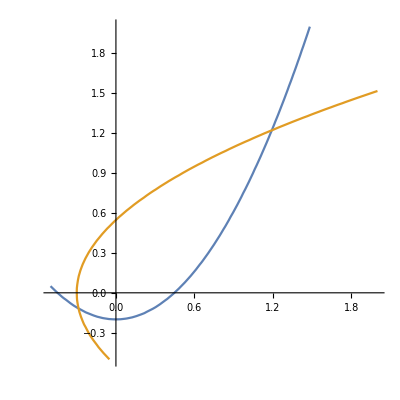

```mathematica
(*graficar para poder encontrar puntos iniciales*)
ContourPlot[{x^2-y-0.2 ==0, y^2-x-0.3==0},{x,-0.5,2},{y,-0.5,2},Frame->False,Axes->True]
```

```mathematica
(*definimos las funciones*)
f=({{x^2-y-0.2}, {y^2-x-0.3}});x0=({{1.18}, {1.23}});
Table[feva= f/.{x->x0[[1,1]],y->x0[[2,1]]};
jac=({{D[f[[1,1]], x], D[f[[1,1]], y]}, {D[f[[2,1]], x], D[f[[2,1]], y]}});
jaceva=jac/.{x->x0[[1,1]],y->x0[[2,1]]};

x0=x0-Inverse[jaceva].feva,{3}];
x0
```

(1.19231
1.2216)

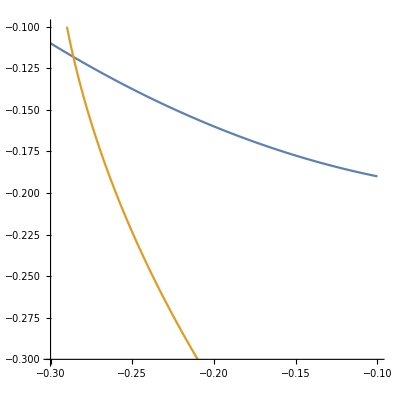

```mathematica
(*graficar para poder encontrar puntos iniciales*)
ContourPlot[{x^2-y-0.2 ==0, y^2-x-0.3==0},{x,-0.3,-0.1},{y,-0.3,-0.1},Frame->False,Axes->True]
```

```mathematica
(*definimos las funciones*)
f=({{x^2-y-0.2}, {y^2-x-0.3}});x0=({{-0.28}, {-0.12}});
Table[feva= f/.{x->x0[[1,1]],y->x0[[2,1]]};
jac=({{D[f[[1,1]], x], D[f[[1,1]], y]}, {D[f[[2,1]], x], D[f[[2,1]], y]}});
jaceva=jac/.{x->x0[[1,1]],y->x0[[2,1]]};

x0=x0-Inverse[jaceva].feva,{6}];
x0
```

(-0.286032
-0.118186)

#### ejercicio 12

```mathematica
$PrePrint=TraditionalForm
```

TraditionalForm

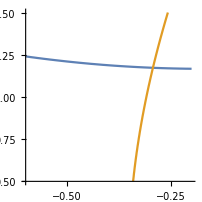

```mathematica
(*graficar para poder encontrar puntos iniciales*)
ContourPlot[{1+x^2-y^2+ⅇ^x Cos[y]==0, 2x y+ⅇ^x Sin[y]==0},{x,-0.6,-0.2},{y,0.5,1.5},Frame->False,Axes->True]
```

```mathematica
(*definimos las funciones*)
f=({{1+x^2-y^2+ⅇ^x Cos[y]}, {2x y+ⅇ^x Sin[y]}});x0=({{-0.3}, {1.2}});
Table[feva= f/.{x->x0[[1,1]],y->x0[[2,1]]};
jac=({{D[f[[1,1]], x], D[f[[1,1]], y]}, {D[f[[2,1]], x], D[f[[2,1]], y]}});
jaceva=jac/.{x->x0[[1,1]],y->x0[[2,1]]};

x0=x0-Inverse[jaceva].feva,{2}];
x0
```

(-0.293163
1.17266)

#### ejercicio 15

```mathematica
(*para 3*)
f=({{x y-z^2-1}, {x y z-x^2+y^2-2}, {ⅇ^x-ⅇ^y+z-3}});x0=({{1.5}, {1.5}, {1.1}});
Table[feva= f/.{x->x0[[1,1]],y->x0[[2,1]],z-> x0[[3,1]]};
jac=({{D[f[[1,1]], x], D[f[[1,1]], y], D[f[[1,1]], z]}, {D[f[[2,1]], x], D[f[[2,1]], y], D[f[[2,1]], z]}, {D[f[[3,1]], x], D[f[[3,1]], y], D[f[[3,1]], z]}});
jaceva=jac/.{x->x0[[1,1]],y->x0[[2,1]],z->x0[[3,1]]};

x0=x0-Inverse[jaceva].feva,{3}];
x0
```

(1.77767
1.42396
1.23747)